# Rooftop Recognition for Solar Energy Potential

Last modified on: Sunday, July 8, 2018 at 17:15

The aim of this project is to detect the rooftop of buildings to determine the available area at different locations and to identify the most suitable ones for solar energy application such as solar PV using Neural Networks and satellite imagery.

## The Data Set

The Inria Aerial Image Labeling addresses a core topic in remote sensing : the automatic pixelwise labeling of aerial imagery.

Dataset features : Coverage of 810 km.b2 (405 km.b2 for training and 405 km.b2 for testing)

Aerial orthorectified color imagery with a spatial resolution of 0.3 m

Ground truth data for two semantic classes : building and not building (publicly disclosed only for the training subset)

Importing

Set the working directory:

```mathematica
SetDirectory["/Volumes/ECG/ProjectWSS/AerialImageDataset/"]
```

/Volumes/ECG/ProjectWSS/AerialImageDataset

Select the images for the input and those for the results:

```mathematica
trainFilesInput=Select[FileNames["train/images/*.tif"],!StringMatchQ[#,___~~"._"~~___]&];
trainFilesResult=StringReplace[#,"train/images/"->"train/gt/"]&/@trainFilesInput;
```

Import an image to test:

```mathematica
imgInput=Import[trainFilesInput⟦1⟧];
imgResult=Import[trainFilesResult⟦1⟧];
```

Partition of the images in 100 from a 5000x5000 to images 500x500 :

```mathematica
splicesInput=Join@@ImagePartition[imgInput,500];
splicesResults=Join@@ImagePartition[imgResult,500];
```

Check the size of the file:

```mathematica
Round[ImageData[splicesResults⟦10⟧]] // ByteCount
```

2000152

Due to the Join we have a list of 100 files that contain the 10x10 images that compose the original:

```mathematica
Length[splicesInput]
```

100

## Assemble Images

```mathematica
assambleImage=ImageAssemble[splicesInput⟦41;;50⟧]
```

-Graphics-

```mathematica
assambleMask=ImageAssemble[Image/@Round[ImageData/@splicesResults⟦41;;50⟧]]
```

-Graphics-

## Compose

Compose the images to see if the image match.

```mathematica
ImageCompose[assambleImage,{assambleMask,0.5}]
```

-Graphics-

```mathematica
ImageCompose[splicesInput⟦10⟧,{splicesResults⟦10⟧,0.5}]
```

-Graphics-

## Association

```mathematica
mxTrain=Thread[splicesInput-> splicesResults];
```

```mathematica
ImageCompose[Keys[mxTrain⟦20⟧],{Values[mxTrain⟦20⟧],0.4}]
```

-Graphics-

First try to export the MX file:

```mathematica
Export["File.mx",mxTrain]
```

File.mx

## mxFileCreator

Function that creates a File per each high resolution image:

```mathematica
mxFileCreator[trainFilesInput_,trainFilesResult_,i_]:=Block[
	{Flag,imgInput,imgResult,splicesInput,splicesResults,mxTrain},

	Flag=TextString[i];

	imgInput=Import[trainFilesInput];
	imgResult=Import[trainFilesResult];

	splicesInput=Join@@ImagePartition[imgInput,500];
	splicesResults=Round[ImageData/@(Join@@ImagePartition[imgResult,500])];

	mxTrain=Thread[splicesInput-> splicesResults];

	Export["train/MXFiles/File"<>Flag<>".mx",mxTrain]
]
```

Try the function

```mathematica
mxFileCreator[trainFilesInput⟦1⟧,trainFilesResult⟦1⟧,1]
```

train/MXFiles/File1.mx

```mathematica
file=Import["train/MXFiles/File1.mx"];
file⟦RandomInteger[{1,100}]⟧
```

-Graphics-→{1}
 |  |  |  |

```mathematica
rand=RandomInteger[{1,100}];
ImageCompose[Keys[file⟦rand⟧],{Image[Values[file⟦rand⟧]],0.5}]
```

-Graphics-

To Map all the images and convert them into association in a MX files :

MapIndexed[mxFileCreator[#[[1]], #[[2]], Echo[#2[[1]]]] &, Transpose[{trainFilesInput, trainFilesResult}]]

## Importing the created files

```mathematica
rand=RandomInteger[{1,100}];
```

Import the MX file created:

```mathematica
fileImported=Import@RandomSample[FileNames["train/MXFiles/*.mx"],rand]⟦1⟧;
```

Test the image association

```mathematica
ImageDimensions[Keys[fileImported][[rand]]]
Dimensions[Values[fileImported][[rand]]]
```

{500,500}

{500,500}

```mathematica
ImageCompose[Keys[fileImported]⟦rand⟧,{Values[fileImported]⟦rand⟧//Image,0.5}]
```

-Graphics-

## The net

Net selection

The net selected for this project was at Wolfram Neural Net Repository for Semantic Segmentation. Released in 2016 by the University of Adelaide, Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data was modify to identify two classes instead of 21.

Take the net model for Semantic Segmentation from the repositiories:

```mathematica
netModel=NetModel["Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data"]
```

NetChain[<>]

## Modify the Input for the size of the images

Replace the encoder to accept images 500x500:

```mathematica
netModel500=NetReplacePart[netModel,"Input"->NetEncoder[{"Image",{500,500},"MeanImage"-> {0.485,0.456,0.406}}] ]
```

NetChain[<>]

### Resize the layers

Drop the last three layer to modify the net:

```mathematica
firstPartNet=NetDrop[netModel500,-3]
```

NetChain[<>]

Add a convolution layer to have two outputs:

```mathematica
convLayer=NetChain[{firstPartNet,ConvolutionLayer[2,{3,3},"Stride"-> {1,1},"PaddingSize"-> {12,12},"Dilation"-> {12,12}],ResizeLayer[{500,500}]}];
```

Take the last two layers from the one with the new encoder:

```mathematica
lastPartNet=NetReplacePart[NetTake[netModel500,-2],"Input"->Automatic]
```

NetChain[<>]

Append the last layers and Softmax Layer with a net decoder of classes:

```mathematica
finalNet=NetAppend[convLayer,{lastPartNet⟦1⟧,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{0,1},"InputDepth"->3}]]
```

NetChain[<>]

Initialize the final net to check for errors:

```mathematica
iniFinalNet=NetInitialize[finalNet]
```

NetChain[<>]

Test the encoders and decoders of the initialize net:

```mathematica
Image[iniFinalNet[Keys[fileImported]⟦rand⟧],ImageSize->Small]
```

-Graphics-

## Loss

Connect the final net to a loss function:

```mathematica
LossNet=NetGraph[<|"eval"->finalNet,"loss"->CrossEntropyLossLayer["Index"]|>,{"eval"->"loss"} ]
```

NetGraph[<>]

Initialize the LossNet:

```mathematica
iniLossNet=NetInitialize[LossNet]
```

NetGraph[<>]

Export the complete net for training:

```mathematica
Export["/Volumes/ECG/ProjectWSS/iniLossNet.wlnet",iniLossNet]
```

/Volumes/ECG/ProjectWSS/iniLossNet.wlnet

Test the LossNet:

```mathematica
iniLossNet[<|"Input"-> fileImported⟦2,1⟧,"Target"-> fileImported⟦2,2⟧|>]
```

0.559258

```mathematica
iniLossNet[fileImported⟦2⟧]
```

0.559258

## Generator function

Fix Data

Set the file path for the MX files:

```mathematica
path="/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/";
mxFiles=FileNames[path<>"*.mx"];
RandomSample[mxFiles,1]⟦1⟧
```

/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/File125.mx

## Binary Files

### Binary write

Binary write:

```mathematica
binaryWrite[file_,expr_]:=With[{bytes=BinaryWrite[file,BinarySerialize[expr]]},Close[file];
bytes]
```

### Import and Reexport Function

Function to convert TIF images to JPG and matrix to Binary:

```mathematica
importAndReExport[path_,folder_]:=Block[{imported,imgs,masks,hashes},
	imported=Import[path];
	imgs=imported[[All,1]];
	masks=imported[[All,2]];
	hashes=Hash/@imgs;
	
	Print[MapThread[Export[folder<>"/"<>ToString[#1]<>".jpg",#2]&,{hashes,imgs}];//AbsoluteTiming];
	Print[MapThread[binaryWrite[folder<>"/"<>ToString[#1]<>".bin",#2]&,{hashes,masks}];//AbsoluteTiming];
	
	Clear[imported,imgs,masks,hashes]
]
```

Take each MX file and create the correspondent JPG and BIN file :

Table[importAndReExport[mxFiles[[i]], “binFiles”], {i, 1, Length[mxFiles], 1}]

### Binary Read

Read the binary file and Deserialize the file:

```mathematica
BinaryDeserialize[ReadByteArray["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/binFiles/712275997646377.bin"]]//Dimensions
```

{500,500}

```mathematica
FileNames["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/binFiles/*.bin"]//Length
```

18000

## Training Out of Core

## Partitional Function

### Data imported

Take the name of the JPG and BIN files:

```mathematica
trainingDataSet={FileNames["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/binFiles/*.jpg"], FileNames["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/binFiles/*.bin"]};
```

Set the data to train:

```mathematica
imageDataSet=Table[File[trainingDataSet[[1,i]]],{i,10}];
imageDataSet//ByteCount
```

1800

```mathematica
maskDataSet=Table[ReadByteArray[trainingDataSet[[2,i]]],{i,10}];
maskDataSet//ByteCount
```

2501170

Associate the image with his respective mask and take a random sample:

```mathematica
data=RandomSample@Thread[imageDataSet->maskDataSet];
data⟦2⟧
```

File[/Volumes/ECG/ProjectWSS/AerialImageDataset/train/MXFiles/binFiles/1003159595019595696.jpg]→ByteArray[…]

Generator

In order to train the net with a big amount of data a generator function was created. The generator function load a single batch of data from an external source to train each time. NetTrain[net, f, …] calls f at each training batch iteration, thus only keeping a single batch of training data in memory. The function can depend on the batch size, which can be set or set automatic by the computer, the absolute batch that is the number of batches load during the training and the round.

partGenerator associate and load a batch of size BatchSize into the net training. In order to do so it takes partitions of the whole dataset in batches of size BatchSize and load the element of this partition taking the module of the AbsoluteBatch. The function also adds one to the mask matrix to get the right values for the net:

```mathematica
partGenerator=Function[Block[{batch,dataSet,batchData},
	If[!ValueQ[partitionedData],partitionedData=Partition[Range[Length[data]],#BatchSize,#BatchSize,1]];
	Print[Association@Thread[Keys[#]->Values[#]]];
	batch=Mod[#AbsoluteBatch,Floor[Length@data/#BatchSize]];
	batchData=data⟦partitionedData[[Echo@(batch+1)]]⟧;
	
	Thread[Keys[batchData]->1+BinaryDeserialize/@Values[batchData]]
	(*<|"Input"->Keys[batchData],"Target"->BinaryDeserialize/@Values[batchData]|>*)
]
];
```

#### Test of partGenerator

```mathematica
Clear[partitionedData]
```

```mathematica
Animate[partGeneratorData=partGenerator[<|"BatchSize"->2,"Round"->0,"AbsoluteBatch"->i|>];
Keys[partGeneratorData],{i,1,10,1}]
```

```mathematica
partGeneratorData⟦1,2⟧//Flatten//DeleteDuplicates
```

{1,2}

### Test

```mathematica
ClearAll[partitionedData];
```

```mathematica
iniLossNet=Import["/Volumes/ECG/ProjectWSS/iniLossNet.wlnet"]
```

NetGraph[<>]

```mathematica
checkpointDir="/Volumes/ECG/ProjectWSS/AerialImageDataset/checkpoint"
```

/Volumes/ECG/ProjectWSS/AerialImageDataset/checkpoint

Net training

```mathematica
iniLossTrainNet=NetTrain[iniLossNet,{partGenerator,"RoundLength"->3},All,MaxTrainingRounds->3,TrainingProgressCheckpointing->{"Directory",checkpointDir}]
```

NetTrain::netmem2: Insufficient memory to evaluate the network: at least 3.21 gigabytes are required but only 2.33 gigabytes are available for TargetDevice -> CPU.

$Failed

Trained Net

#### Encoder & Decoder

Set the encoder and decoders for the trained net :

Set the encoder for image size 500x500 and a MeanImage:

```mathematica
enc=NetEncoder[{"Image",{500,500},"MeanImage"-> {0.485,0.456,0.406}}];
```

Set the decoder for the classe which 0 means no rooftop and 1 means rooftop:

```mathematica
dec=NetDecoder[{"Class",{0,1},"InputDepth"->3}];
```

Import the trained net as an object:

```mathematica
finalTrainedNet=Import["/Volumes/ECG/ProjectWSS/AerialImageDataset/TrainedNets/model_3740226865.mx"]
```

NetTrainResultsObject[<>]

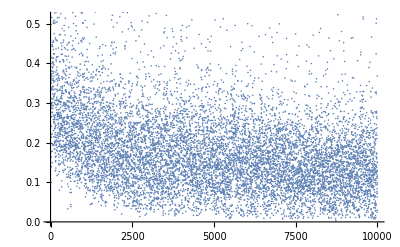

```mathematica
ListPlot[finalTrainedNet["BatchLossList"]]
```

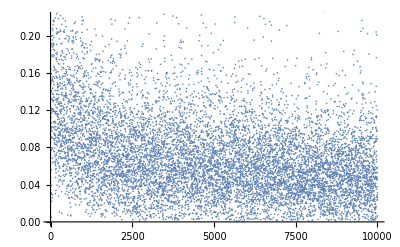

```mathematica
ListPlot[finalTrainedNet["BatchErrorRateList"]]
```

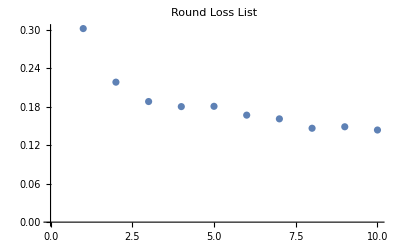

```mathematica
ListPlot[finalTrainedNet["RoundLossList"],PlotLabel->"Round Loss List"]
```

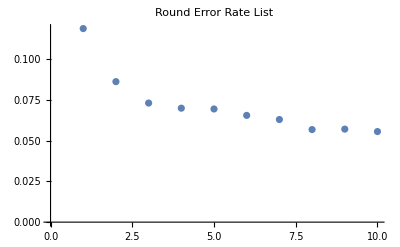

```mathematica
ListPlot[finalTrainedNet["RoundErrorRateList"],PlotLabel->"Round Error Rate List"]
```

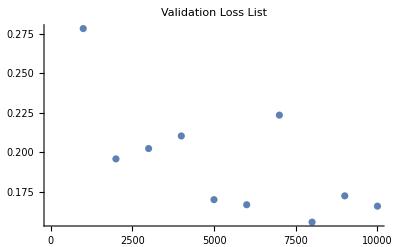

```mathematica
ListPlot[finalTrainedNet["ValidationLossList"],PlotLabel->"Validation Loss List"]
```

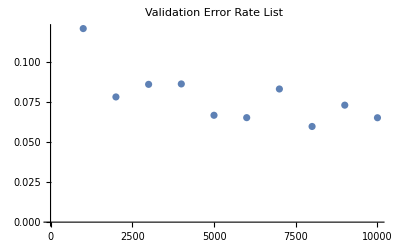

```mathematica
ListPlot[finalTrainedNet["ValidationErrorRateList"],PlotLabel->"Validation Error Rate List"]
```

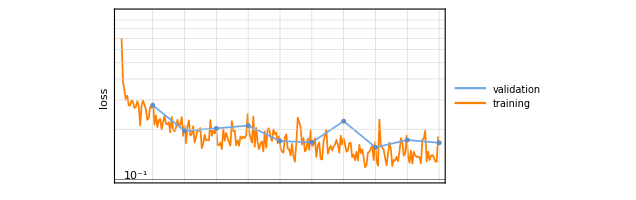

```mathematica
finalTrainedNet["LossEvolutionPlot"]
```

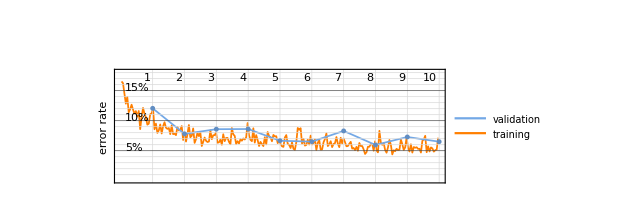

```mathematica
finalTrainedNet["ErrorRateEvolutionPlot"]
```

```mathematica
Transpose@{{Style["Properties",FontSize-> 20],"FinalRoundLoss","FinalRoundErrorRate","FinalValidationLoss","FinalValidationErrorRate","LowestValidationLoss","LowestValidationErrorRate","BatchSize","TotalRounds","TotalBatches","TotalInputs","TotalTrainingTime","MeanBatchesPerSecond","MeanInputsPerSecond","InitialLearningRate","FinalLearningRate","OptimizationMethod"},{Style["Values",FontSize-> 20],finalTrainedNet["FinalRoundLoss"],finalTrainedNet["FinalRoundErrorRate"],finalTrainedNet["FinalValidationLoss"],finalTrainedNet["FinalValidationErrorRate"],finalTrainedNet["LowestValidationLoss"],finalTrainedNet["LowestValidationErrorRate"],finalTrainedNet["BatchSize"],finalTrainedNet["TotalRounds"],finalTrainedNet["TotalBatches"],finalTrainedNet["TotalInputs"],UnitConvert[Quantity[finalTrainedNet["TotalTrainingTime"],"Seconds"],"Hours"],finalTrainedNet["MeanBatchesPerSecond"],finalTrainedNet["MeanInputsPerSecond"],finalTrainedNet["InitialLearningRate"],finalTrainedNet["FinalLearningRate"],finalTrainedNet["OptimizationMethod"]}}//Dataset
```

Dataset[<>]

```mathematica
finalTrainedNetEval=NetExtract[finalTrainedNet["TrainedNet"],"eval"]
```

NetChain[<>]

```mathematica
finalTrainedNetEvalEnc=NetReplacePart[finalTrainedNetEval,"Input"->enc ]
```

NetChain[<>]

```mathematica
finalTrainedNetEvalDec=NetReplacePart[finalTrainedNetEvalEnc,"Output"->dec ]
```

NetChain[<>]

```mathematica
Export["/Volumes/ECG/ProjectWSS/AerialImageDataset/FinalTrainedNetEval.mx",finalTrainedNetEvalDec]
```

/Volumes/ECG/ProjectWSS/AerialImageDataset/FinalTrainedNetEval.mx

## Net Evaluation

### File

```mathematica
TestImage=Import["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/images/austin1.tif"];
```

```mathematica
imageToTest=ImagePartition[TestImage,{500,500}];
```

```mathematica
rand1=RandomInteger[{1,10}];
rand2=RandomInteger[{1,10}];
```

```mathematica
ImageCompose[imageToTest⟦rand1,rand2⟧,{Image[finalTrainedNetEvalDec[imageToTest⟦rand1,rand2⟧]],0.5}]
```

GeoImage

```mathematica
testImage[latitud_,longitud_,net_]:=Module[{geoImage,geoImageResize},
geoImage=GeoImage[GeoPosition[{latitud,longitud}],GeoRange->Quantity[75, "Meters"],GeoProjection->"Mercator",ImageSize->Small];
geoImageResize=ImageResize[geoImage,{500,500}];
{ImageCompose[geoImageResize,{Image[net[geoImageResize]],0.3}]
,Image[net[geoImageResize]]}]
```

```mathematica
GeoPosition[Entity["City",{"SanLuisPotosi","SanLuisPotosi","Mexico"}]]
```

GeoPosition[{22.16,-100.98}]

```mathematica
Manipulate[testImage[22.16+u,-100.98+u,finalTrainedNetEvalDec],{u,{-10,-10},{10,10}},ControlType->Slider2D,ControlPlacement->Left]
```

```mathematica
ImageMeasurements[Image[finalTrainedNetEvalDec[imageToTest⟦rand1,rand2⟧]],"Mean"]
```

0.138952

```mathematica
testImage[22.16+10,-100.98+10,finalTrainedNetEvalDec]
```

{-Graphics-,-Graphics-}

## Image Matrix

```mathematica
ImageMeasurements[areaTest,"Mean"]
```

0.130916

```mathematica
(500*.30)^2
```

22500.

```mathematica
% ImageMeasurements[areaTest,"Mean"]
```

2945.61

```mathematica
roofPixels=Count[Flatten[ImageData@areaTest],1.]
```

32729

```mathematica
totalPixels=Times@@ImageDimensions[areaTest]
```

250000

```mathematica
percentageOfRoof=roofPixels/totalPixels 100//N
```

13.0916

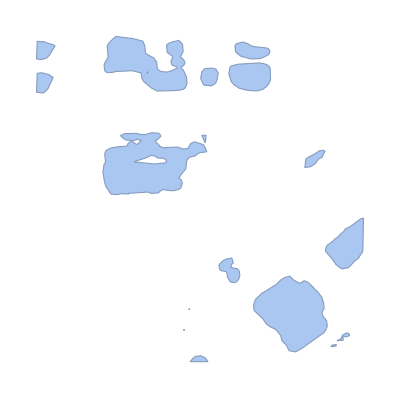

```mathematica
ImageMesh[areaTest]
```

```mathematica
per
```

```mathematica
ImageData@
```

```mathematica
EdgeDetect[areaTest]
```

-Graphics-

```mathematica
GeoImage
```

## Google Images

```mathematica
GetSatImage[x_,y_,zoom_,range_]:=Image[GeoGraphics[GeoPosition[{x,y}],GeoServer->{"http://mt0.google.com/vt/lyrs=s&x=`2`&y=`3`&z=`1`"},GeoRange->Quantity[range,"Meters"],GeoZoomLevel->zoom]];
GetStreetImage[x_,y_,zoom_,range_]:=Image[GeoGraphics[GeoPosition[{x,y}],GeoBackground->GeoStyling["StreetMapNoLabels"],GeoRange->Quantity[range,"Meters"],GeoZoomLevel->zoom]];
```

```mathematica
Here
```

GeoPosition[{42.37,-71.24}]

```mathematica
GetSatImage[42.37,-71.24,50,1050]
```

-Graphics-

```mathematica
GetStreetImage[42.37,-71.24,10,150]
```

-Graphics-